### Conformal diagram for proper time coordinates (i.e., ds^2=-dt^2 + Exp(2t) dr^2)

```mathematica
r[T_,θ_]:=Sin[θ]/(Sin[T]+Cos[θ]);
t[T_,θ_]:=Log[(Sin[T]+ Cos[θ])/Cos[T]];
```

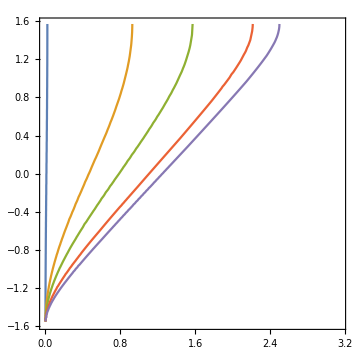

```mathematica
(*Constant r plot for entire dS*)
ContourPlot[{r[T,θ]==1/100,r[T,θ]==1/2,r[T,θ]==1,r[T,θ]==2,r[T,θ]==3},{θ,0,Pi},{T,-Pi/2,Pi/2-0.00001},ImageSize->Medium]
```

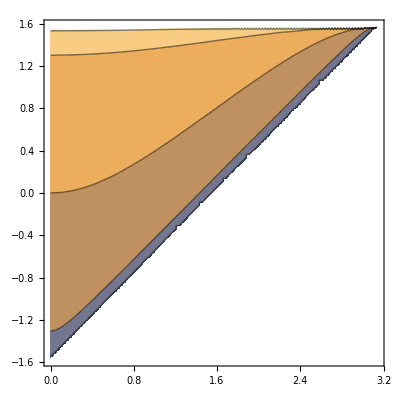

```mathematica
(*constant t in planar coordinates for half of dS*)
ContourPlot[t[T,θ],{θ,0,Pi},{T,-Pi/2,Pi/2}]
```

### Conformal diagram for conformal time coordinate η

```mathematica
η[T_,θ_]:=-1/((Sin[T]+ Cos[θ])/Cos[T])
```

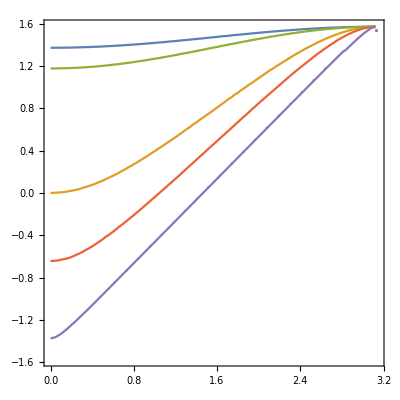

```mathematica
(*constant eta in Poincare coordinates for half of dS*)
ContourPlot[{η[T,θ]==-0.1,η[T,θ]==-1,η[T,θ]==-0.2,η[T,θ]==-2,η[T,θ]==-10},{θ,0,Pi},{T,-Pi/2,Pi/2-0.000001}]
```

## Plotting worldlines

#### Standard way as (\eta, x) plots

```mathematica
eta[t_]:=c4/(Cos[c1 t+c2]);
x[t_]:=c4 Tan[c2+c1 t]+c3;
solconst=Solve[{eta[0]==EA,eta[1]==EB,x[0]==XA,x[1]==XB},{c1,c2,c3,c4}]/.{C[1]->0,C[2]->0}//Simplify;
```

```mathematica
solINI=Simplify[solconst,XB>XA>0&&EA<EB<0]
```

{{c3→(-EA^2+EB^2+XA^2-XB^2)/(2 (XA-XB)),c4→-(√(-EA^4-(EB^2-(XA-XB)^2)^2+2 EA^2 (EB^2+(XA-XB)^2)))/(2 (XA-XB)),c1→ArcTan[EA^2+EB^2-(XA-XB)^2,√(-EA^4-(EB^2-(XA-XB)^2)^2+2 EA^2 (EB^2+(XA-XB)^2))],c2→ArcTan[-√(-EA^4-(EB^2-(XA-XB)^2)^2+2 EA^2 (EB^2+(XA-XB)^2)),EA^2-EB^2+(XA-XB)^2]},{c3→(-EA^2+EB^2+XA^2-XB^2)/(2 (XA-XB)),c4→(√(-EA^4-(EB^2-(XA-XB)^2)^2+2 EA^2 (EB^2+(XA-XB)^2)))/(2 (XA-XB)),c1→ArcTan[EA^2+EB^2-(XA-XB)^2,-√(-EA^4-(EB^2-(XA-XB)^2)^2+2 EA^2 (EB^2+(XA-XB)^2))],c2→ArcTan[√(-EA^4-(EB^2-(XA-XB)^2)^2+2 EA^2 (EB^2+(XA-XB)^2)),EA^2-EB^2+(XA-XB)^2]}}

```mathematica
param={EA->-5,EB->-5,XA->0,XB->9};
param2={EA->-5,EB->-5,XA->0,XB->11};
param3={EA->-5,EB->-5,XA->0,XB->1};
param4={EA->-1,EB->-1,XA->0,XB->1};
param5={EA->-1/4,EB->-1/4,XA->0,XB->1/10};
```

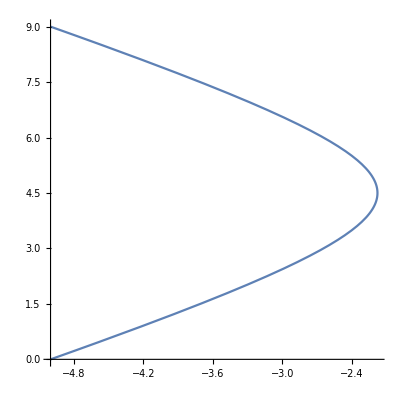

```mathematica
ParametricPlot[{eta[t],x[t]}/.solINI[[1]]/.param,{t,0,1},AspectRatio->1]
```

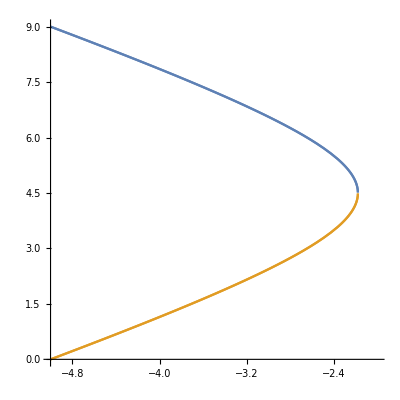

```mathematica
Plot[{Sqrt[η^2-c4^2]+c3/.solINI/.param,-Sqrt[η^2-c4^2]+c3/.solINI/.param},{η,-5,-2},AspectRatio->1]
```

#### In conformal diagrams

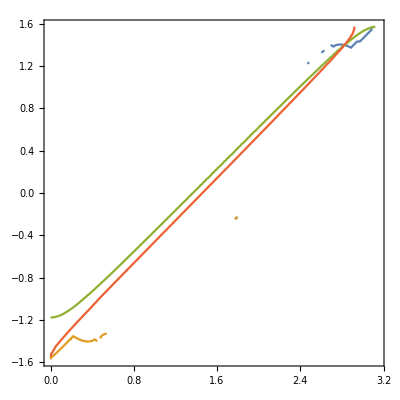

```mathematica
ContourPlot[{r[T,θ]==(Sqrt[η[T,θ]^2-c4^2]+c3/.solINI[[1]]/.param),r[T,θ]==-(Sqrt[η[T,θ]^2-c4^2]+c3/.solINI[[1]]/.param),η[T,θ]==-5,r[T,θ]==9},{θ,0,Pi},{T,-Pi/2,Pi/2-0.000001},WorkingPrecision->30]
```

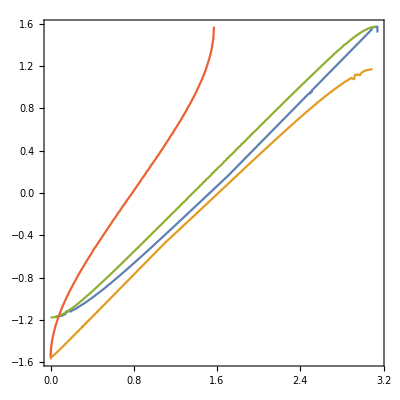

```mathematica
ContourPlot[{r[T,θ]==(Sqrt[η[T,θ]^2-c4^2]+c3/.solINI[[1]]/.param3),r[T,θ]==-(Sqrt[η[T,θ]^2-c4^2]+c3/.solINI[[1]]/.param3),η[T,θ]==-5,r[T,θ]==1},{θ,0,Pi},{T,-Pi/2,Pi/2-0.000001},WorkingPrecision->30]
```

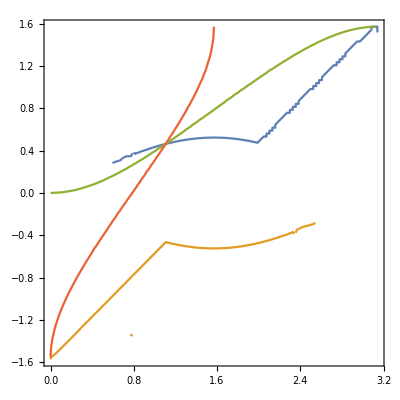

```mathematica
ContourPlot[{r[T,θ]==(Sqrt[η[T,θ]^2-c4^2]+c3/.solINI[[1]]/.param4),r[T,θ]==-(Sqrt[η[T,θ]^2-c4^2]+c3/.solINI[[1]]/.param4),η[T,θ]==-1,r[T,θ]==1},{θ,0,Pi},{T,-Pi/2,Pi/2-0.000001},WorkingPrecision->30]
```

```mathematica
ContourPlot[{r[T,θ]==(Sqrt[η[T,θ]^2-c4^2]+c3/.solINI[[1]]/.param),r[T,θ]==-(Sqrt[η[T,θ]^2-c4^2]+c3/.solINI[[1]]/.param),η[T,θ]==-5,r[T,θ]==9},{θ,0,Pi},{T,-Pi/2,Pi/2-0.000001},WorkingPrecision->30]
```

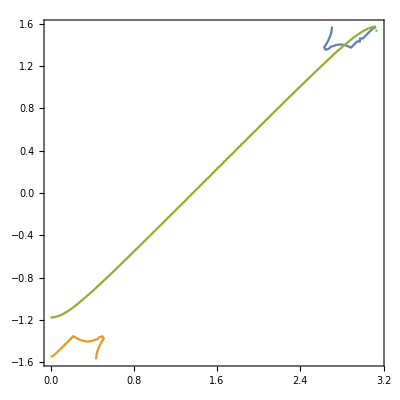

```mathematica
ContourPlot[{r[T,θ]==Re[(Sqrt[η[T,θ]^2-c4^2]+c3/.solINI[[1]]/.param)],r[T,θ]==-Re[(Sqrt[η[T,θ]^2-c4^2]+c3/.solINI[[1]]/.param)],η[T,θ]==-5},{θ,0,Pi},{T,-Pi/2,Pi/2-0.000001}]
```

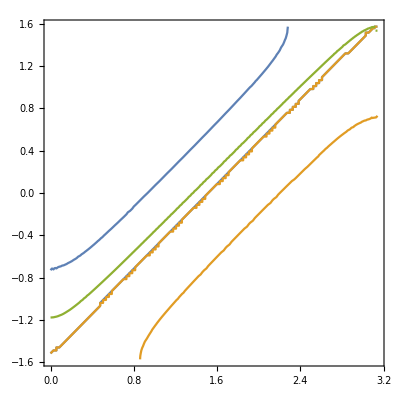

```mathematica
ContourPlot[{r[T,θ]==Im[(Sqrt[η[T,θ]^2-c4^2]+c3/.solINI[[1]]/.param)],r[T,θ]==-Im[(Sqrt[η[T,θ]^2-c4^2]+c3/.solINI[[1]]/.param)],η[T,θ]==-5},{θ,0,Pi},{T,-Pi/2,Pi/2-0.000001}]
```

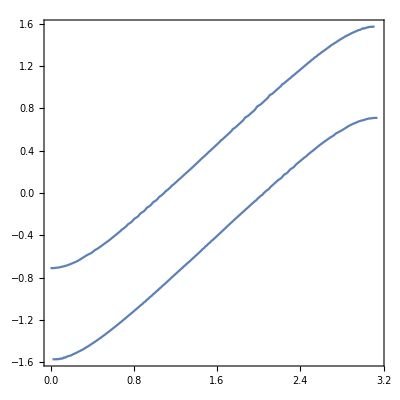

```mathematica
ContourPlot[{-19/4+Cos[T]^2/(Cos[θ]+Sin[T])^2==0},{θ,0,Pi},{T,-Pi/2,Pi/2-0.000001}]
```